## Generating 5-fold symmetry axis on 2D surface

n= 1

```mathematica
a1 = Cos[2π/5];
b1 = Cos[π/5];
c1 = Sin[2π/5];
d1 = Sin[4π/5];
vertices={{a1,-c1}, {1,0}, {a1,c1}, {-b1,d1}, {-b1,-d1}};
transv1 = {{a1+1,-c1}, {1+1,0}, {a1+1,c1}, {-b1+1,d1}, {-b1+1,-d1}};
```

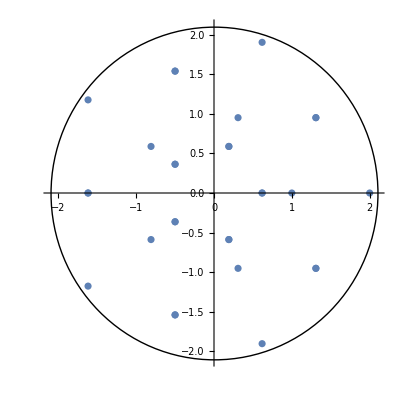

```mathematica
rotv1 = RotationTransform[2π/5, {0,0}] /@ # &@transv1;
rotv2 = RotationTransform[2π/5, {0,0}] /@ # &@rotv1;
rotv3 = RotationTransform[2π/5, {0,0}] /@ # &@rotv2;
rotv4 = RotationTransform[2π/5, {0,0}] /@ # &@rotv3;
n1point = ListPlot[Join[vertices, transv1, rotv1, rotv2, rotv3, rotv4], AspectRatio->1];
circle = Graphics[Circle[{0, 0}, 2.1]];
n1 = Show[n1point, circle, PlotRange-> All]
```

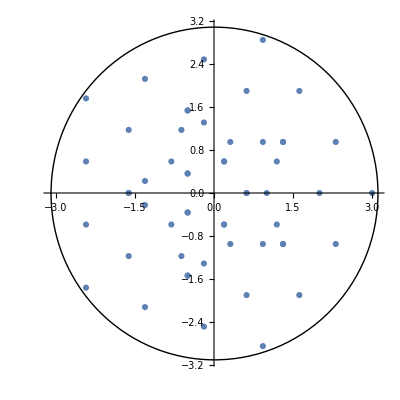

```mathematica
a1 = Cos[2π/5];
b1 = Cos[π/5];
c1 = Sin[2π/5];
d1 = Sin[4π/5];
vertices={{a1,-c1}, {1,0}, {a1,c1}, {-b1,d1}, {-b1,-d1}};
transv1 = {{a1+1,-c1}, {1+1,0}, {a1+1,c1}, {-b1+1,d1}, {-b1+1,-d1}};
rotv1 = RotationTransform[2π/5, {0,0}] /@ # &@transv1;
rotv2 = RotationTransform[2π/5, {0,0}] /@ # &@rotv1;
rotv3 = RotationTransform[2π/5, {0,0}] /@ # &@rotv2;
rotv4 = RotationTransform[2π/5, {0,0}] /@ # &@rotv3;
transv2 = {{a1+2,-c1}, {1+2,0}, {a1+2,c1}, {-b1+2,d1}, {-b1+2,-d1}};
rotv5 = RotationTransform[2π/5, {0,0}] /@ # &@transv2;
rotv6 = RotationTransform[2π/5, {0,0}] /@ # &@rotv5;
rotv7 = RotationTransform[2π/5, {0,0}] /@ # &@rotv6;
rotv8 = RotationTransform[2π/5, {0,0}] /@ # &@rotv7;
n2point = ListPlot[Join[vertices, transv1, rotv1, rotv2, rotv3, rotv4, transv2, rotv5, rotv6, rotv7, rotv8], AspectRatio->1];
circle2 = Graphics[Circle[{0, 0}, 3.1]];
n2 = Show[n2point, circle2, PlotRange-> All]
```

## Loading data

import data string:

```mathematica
data = Import["/Users/Jihyeon/Desktop/3j3i.pdb1","String"];
```

replace negative signs(-) with spaces to separate columns:

```mathematica
spaced  = StringReplace[data,"-"-> " -"];
```

export modified file to directory as text:

```mathematica
Export["/Users/Jihyeon/Desktop/3j3i_spaced.txt",spaced];
```

open modified file:

```mathematica
str = OpenRead["/Users/Jihyeon/Desktop/3j3i_spaced.txt"];
```

Read data starting from row 180:

```mathematica
Do[Read[str,"String"],154]
```

```mathematica
Read[str,"String"]
```

VVAMLCGQTETNLIPSHHYGKAFAPLFASNAMFTRNQRAVITREAFVCARSAVAQCQDAGFLVPRPLDALRQFDVTSAAA

read the list as words

```mathematica
fullrecord=ReadList[str,"Word", RecordLists->True];
```

split the list when consecutive first letter appears:

```mathematica
splitted = Split[fullrecord,First[#1]===First[#2]&];
```

remove unnecessary rows:

```mathematica
removed = DeleteCases[splitted,x_/;First[First[x]]== "TER"];
removed = DeleteCases[removed,x_/;First[First[x]]== "HETATM"];
removed = DeleteCases[removed,x_/;First[First[x]]== "MODEL"];
removed = DeleteCases[removed,x_/;First[First[x]]== "ENDMDL"];
removed = DeleteCases[removed,x_/;First[First[x]]== "MASTER"];
removed = DeleteCases[removed,x_/;First[First[x]]== "END"];
```

```mathematica
Dimensions[removed]
```

{60}

## Calculating center of mass

### extracting coordinates

only extract atom data and coordinates:

```mathematica
atom =   removed⟦All,All, -1⟧;
```

replace atoms with its atomic mass:

```mathematica
mass = atom/.{"N"->14.00, "C" -> 12.01, "O" -> 15.99, "S" -> 32.06};
```

extract x,y,z coordinates:

```mathematica
xcoor =  ToExpression[removed⟦All,All, 7⟧]
```

{1}
 |  |  |  |

```mathematica
ycoor =  ToExpression[removed⟦All,All, 8⟧]
```

{1}
 |  |  |  |

```mathematica
zcoor =  ToExpression[removed⟦All,All, 9⟧]
```

{1}
 |  |  |  |

### Calculation

equation for calculating center of mass:

```mathematica
calcx[mass_,xcoor_] :=Sum[mass[[i]]* xcoor[[i]], {i, Length[mass]}]  /Sum[mass[[i]],{ i, Length[mass]}]
```

```mathematica
xset = MapThread[calcx, {mass, xcoor}];
```

```mathematica
calcy[mass_,ycoor_] :=Sum[mass[[i]]* ycoor[[i]], {i, Length[mass]}]  /Sum[mass[[i]],{ i, Length[mass]}]
```

```mathematica
yset = MapThread[calcy, {mass, ycoor}];
```

```mathematica
calcz[mass_,zcoor_] :=Sum[mass[[i]]* zcoor[[i]], {i, Length[mass]}]  /Sum[mass[[i]],{ i, Length[mass]}]
```

```mathematica
zset = MapThread[calcz, {mass, zcoor}];
```

put all x, y, z coordinates together:

```mathematica
totcoor[xset_,yset_,zset_] :=List[xset, yset, zset]
centercoor = MapThread[totcoor, {xset, yset, zset}];
```

```mathematica
ListPointPlot3D[centercoor, BoxRatios->{1, 1, 1}, LabelingFunction->Automatic]
```

-Graphics3D-

```mathematica
ListSurfacePlot3D[centercoor, BoxRatios->{1, 1, 1}]
```

-Graphics3D-

```mathematica
DelaunayMesh[centercoor]
```